# MAT 132 - Calculus II

## Summer II 2019 Mathematics Department Stony Brook University

Instructor: Marlon de Oliveira Gomes

◀     |     ▶

## Integration

### Motivation from geometry: the Area Problem.

Area Problem: to find the area of a planar region bounded by the graph of a positive function.

Simple examples:

A constant function

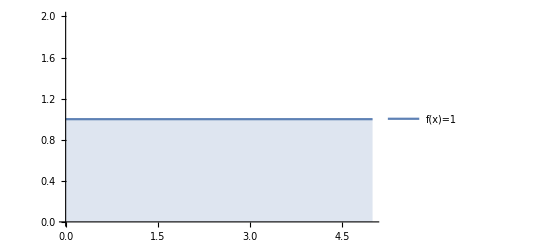

```mathematica
Plot[1,{x,0,5}, Filling->Bottom, PlotLegends->Placed[{"f(x)=1"},Above]]
```

A first-degree polynomial

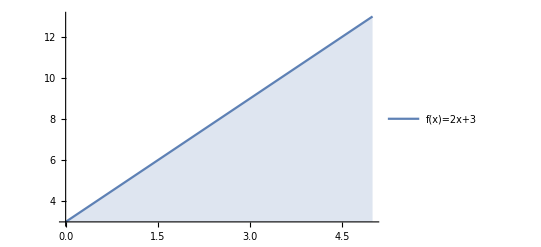

```mathematica
Plot[2x+3, {x,0,5}, Filling->Bottom, PlotLegends->Placed[{"f(x)=2x+3"}, Above]]
```

◀     |     ▶

## Integration

### Motivation from geometry: the Area Problem.

How to estimate area under a the graph of a general positive function?

Idea: use rectangles as an elementary approximation.

Archimedes’ example: the area under a parabola.

```mathematica
Manipulate[
Show[
DiscretePlot[t^2,
{t,0,1,1/2^n},
ExtentSize->Right,
Frame->True,
PlotRange->{{0,1},{0,1}},
PlotRangeClipping-> True],
Plot[t^2,
{t,0,1},
Frame->True,
PlotRange->{{0,1},{0,1}},
PlotRangeClipping-> True,
PlotLegends->Placed[{"f(x)=x^2"},Above]
]
],
{n,1,8,1},
FrameLabel->Style["Left-endpoint approximations",13]]
```

◀     |     ▶

## Integration

### Motivation from Geometry: the Area Problem.

Archimedes’ example (continued): the area under a parabola.

```mathematica
Manipulate[
Show[
DiscretePlot[t^2,
{t,0,1,1/2^n},
ExtentSize->Left,
Frame->True,
PlotRange->{{0,1},{0,1}},
PlotRangeClipping-> True],
Plot[t^2,
{t,0,1},
Frame->True,
PlotRange->{{0,1},{0,1}},
PlotRangeClipping-> True,
PlotLegends->Placed[{"f(x)=x^2"},Above]
]
],
{n,1,8,1},
FrameLabel->Style["Right-endpoint approximations", 13]]
```

◀     |     ▶

## Integration

### Motivation from Geometry: the Area Problem

The idea of approximating the area under graphs was formalized by Riemann. To approximate the area underneath the graph of a positive function “f” within the interval [a,b], we:

subdivide the interval into “n” equally sized subintervals.

select a sample point in each subinterval, whose image is the height of the approximating rectangle.

add the areas of the approximating rectangles.

These sums take the following form:

```mathematica
TraditionalForm[HoldForm[Sum["f(x_i^*)Δx",{i,1,n}]]]
```

∑_(i=1)^n f(x_i^*)Δx

Notation:

“f” is the function whose graph bounds the region in question.

“x_i^*” are the sample points, one for each rectangle.

“Δx” is the width of each rectangle.

Typical sampling points: left-endpoints, midpoints, right-endpoints.

◀     |     ▶

## Integration

### Motivation from Geometry: the Area Problem

#### A comparison between samplings

```mathematica
Manipulate[
Show[
DiscretePlot[t^2,
{t,0,1,1/n},
ExtentSize->Right,
Frame->True,
PlotRange->{{0,1},{0,1}},
PlotRangeClipping-> True],
DiscretePlot[t^2,
{t,0,1,1/n},
ExtentSize->Left,
Frame->True,
PlotRange->{{0,1},{0,1}},
PlotRangeClipping-> True],
Plot[t^2,
{t,0,1},
Frame->True,
PlotRange->{{0,1},{0,1}},
PlotRangeClipping-> True,
PlotLegends->Placed[{"f(x)=x^2"},Above]
]
],
{n,1,20,1}
]
```

This example illustrates the fact that the approximations by left-endpoints (more opaque) and right-endpoints (less opaque) seem to converge to each other, as the number of rectangles grows.

◀     |     ▶

## Integration

### Motivation from Geometry: the Area Problem

One might wonder whether our intuitive idea that all of these approximations will eventually (as the number of rectangles grows) lead to a number. After all, the number of summands grows infinitely large, and there is no telling where their sum will go. To test it, we compute the limits of the approximations, as the number of rectangles goes to infinity:

```mathematica
TraditionalForm[HoldForm[Limit[Sum["f(x_i^*)Δx",{i,1,n}],n-> ∞] ]]
```

(∑_(i=1)^n f(x_i^*)Δx)n∞

Such limits are called Riemann Sums. They can also be defined for functions that change sign, although in this case they no longer represent areas, but rather signed areas, in which case the area of regions below the axis is counted with a negative sign.

#### Definition

A function is called integrable on an interval when all of its Riemann sums (that is, for all possibilities of sampling points) exist and coincide.

An immediate question is how to test integrability - given that testing each sampling is impractical. We will not answer this question in this course. Instead, we shall contempt ourselves with the fact that all continuous functions are integrable.

◀     |     ▶

## Integration

### The Definite Integral

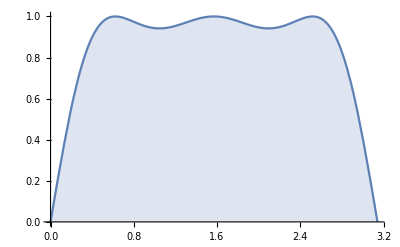

```mathematica
Plot[Sin[x+Sin[2x]],
 {x,0,Pi},
 Filling->Bottom,
PlotLegends->Placed["y=f(x)",Above] ]
```

If a function “f” is integrable in an interval [a,b], we call the limit of its Riemann sums therein its integral on the interval [a,b], represented by

```mathematica
TraditionalForm[Integrate[f[x],{x,a,b}]]
```

∫_a^b f(x)ⅆx

The above integral is read “integral of ‘f’, from ‘a’ to ‘b’, relative to ‘x’”.

◀     |     ▶

## Integration

### The Definite Integral

#### Back to Archimedes: the area under a parabola, by Riemann sums.

In Archimedes example, f(x)=x^2, a=0, b=1. Subdividing this interval into n rectangles yields a width size

Δx=1/n.

Since f is continuous, we can approximate it by any sampling (in the limit, the results are all the same). We use right-endpoints

x_i=i/n.

The Riemann sum is

```mathematica
TraditionalForm[HoldForm[Integrate[x^2,{x,0,1}]==Limit[Sum[i^2/n^3,{i,1,n}],n-> ∞]== Limit[Sum[(n*(n+1)*(2n+1))/(6n^3),{i,1,n}],n-> ∞]==1/3 ]]
```

∫_0^1 x^2 ⅆx==(∑_(i=1)^n i^2/n^3)n∞==(∑_(i=1)^n (n (n+1) (2 n+1))/(6 n^3))n∞==1/3

◀     |     ▶

## Integration

### The Definite Integral

Computing definite integrals from Riemann sums is hard. We’ll study other means of computing integrals in what follows.

#### Properties of integration

Linearity: “f” and “g” integrable functions, “t” a constant

```mathematica
TraditionalForm[Integrate[(f[x]+tg[x]),{x,a,b}]== (Integrate[f[x],{x,a,b}]) +t(Integrate[g[x],{x,a,b}])]
```

∫_a^b (f(x)+tg(x))ⅆx==∫_a^b f(x)ⅆx+t ∫_a^b g(x)ⅆx

Domain additivity: if a<c<b, and the function “f” is integrable on [a,b], then

```mathematica
TraditionalForm[Integrate[f[x],{x,a,b}]== (Integrate[f[x],{x,a,c}]) +(Integrate[f[x],{x,c,b}])]
```

∫_a^b f(x)ⅆx==∫_a^c f(x)ⅆx+∫_c^b f(x)ⅆx

Comparison: if a<b, and f(x) ≤g(x), for all a ≤x≤b, then

```mathematica
TraditionalForm[Integrate[f[x],{x,a,b}]≤ (Integrate[g[x],{x,a,b}])]
```

∫_a^b f(x)ⅆx≤∫_a^b g(x)ⅆx

◀     |     ▶

## Integration

### The Definite Integral

#### The Mean Value Theorem

Suppose the integrand f(x) is a continuous function on the interval [a,b]. Then there exists a number c, between a and b, for which

```mathematica
TraditionalForm[Integrate[f[x],{x,a,b}]== f[c](b-a)]
```

∫_a^b f(x)ⅆx==(b-a) f(c)

The idea behind this theorem is the Intermediate Value Theorem for continuous functions.

```mathematica
Manipulate[
Show[
Plot[Sin[x+Sin[2x]],
 {x,0,Pi},
PlotLegends->Placed["y=f(x) vs y=ℼm",Above],
PlotRange->{{0,Pi},{0,Pi/2}},
PlotRangeClipping-> True ],
Plot[Pi*m,
 {x,0,Pi}, 
Filling->Bottom,
PlotRange->{{0,Pi},{0,Pi/2}},
PlotRangeClipping-> True
]], 
{m,0,1/Pi}]
```

In the example above, we compare the areas underneath the graph of a continuous function f(x), defined on the interval [0,ℼ], and the graphs of the family of constant functions g_m(x)=ℼm (which depend on a parameter m). As m varies between the minimum and maximum values of f, the area under the graph of g_m changes, from a value that is less than the under the graph of  f to a value that is greater than the area under the graph of f. By continuity of the family of functions g_m, relative to the parameter m, there exists a value  m_avg for which the areas underneath f and g_m_avg are equal. In turn, the number m_avg lies between the minium and maximum values of f, thus, by the intermediate value theorem, there exists a number c in the domain of f, for which m_avg=f(c). If follows that

```mathematica
TraditionalForm[Integrate[f[x],{x,0,Pi}]== f[c]*Pi]
```

∫_0^π f(x)ⅆx==π f(c)

## Integration

### The Indefinite Integral

Having seen a few examples and properties of integrals, we turn to study Integration, on its own right.

Given a function f(x), integrable on the interval [a,b], we may consider intervals in intermediate regions.

```mathematica
DynamicModule[{pts={{0,0},{Pi,0}}},LocatorPane[Dynamic[pts,(pts[[1]]={#[[1,1]],0};pts[[2]]={#[[2,1]],0})&],Dynamic[Framed@Show@{Plot[Sin@x,{x,0,2 Pi},PlotLabel->ToString@TraditionalForm[Integrate[sin[x],{x,pts[[1,1]],pts[[2,1]]}]]<>" = "<>ToString[Integrate[Sin@x,{x,pts[[1,1]],pts[[2,1]]}]]],Plot[Sin@x,{x,pts[[1,1]],pts[[2,1]]},PlotRange-> {-1,1},Filling->Axis]}]]]
```

That is, we may define a function by integrating another:

```mathematica
TraditionalForm[g[y]==Integrate[f[x],{x,a,y}]]
```

g(y)==∫_a^y f(x)ⅆx

The function g is called an indefinite integral of f.

◀     |     ▶

## Integration

### The indefinite integral